# Mosaic plots for numerical variables via categorical mapping

In this notebook we show how to transform numerical variables into categorical in order to get more informative mosaic plots.

Load the paclet

```mathematica
Needs["AntonAntonov`MosaicPlot`"]
```

Here we get the Titanic dataset:

```mathematica
dsTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}]
```

Here is a mosaic plot of passenger class vs. passenger age:

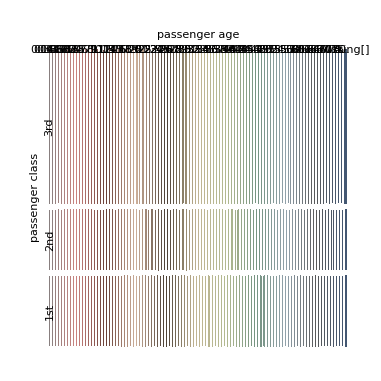

```mathematica
MosaicPlot[dsTitanic[All,{"passenger class","passenger age"}]]
```

The plot is not very informative

Here we make a mapping function of the numerical variable "passenger age" into "categorical age" integers (factors):

```mathematica
factor=Piecewise[{{1,-Infinity<##1<=5},{2,5<##1<=14},{3,14<##1<=21},{4,21<##1<=28},{5,28<##1<=35},{6,35<##1<=50},{7,50<##1<=Infinity}},0]&;
```

Here we make a list of rules that map the categorical integers (factors) into (informative) labels:

```mathematica
aFactorLabel={1->"1(under 6)",2->"2(6...14)",3->"3(15...21)",4->"4(22...]28)",5->"5(29...35)",6->"6(36...50)",7->"7(50+)",0->"0(missing)"};
```

Here we add the column "AgeFactor" that has the mapped values of "passenger age":

```mathematica
dsTitanic2=dsTitanic[All,<|#,"AgeFactor"->If[Head[#["passenger age"]]===Missing,0,factor[#["passenger age"]]]/. aFactorLabel|>&];
```

Here is the mosaic plot of passenger class vs. categorical passenger age:

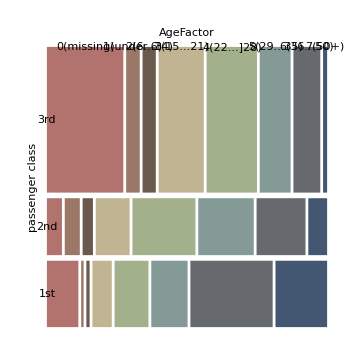

```mathematica
MosaicPlot[dsTitanic2[All,{"passenger class","AgeFactor"}],"LabelRotation"->{1,0.5},ImageSize->Medium]
```

The second mosaic plot is more informative.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/MosaicPlot

AntonAntonov`MosaicPlot`

AntonAntonov/MosaicPlot/tutorial/Mosaicplotsfornumericalvariablesviacategoricalmapping

### Keywords